## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.42; Q=0.997;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.319765+2.89129×10^-10 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.388657

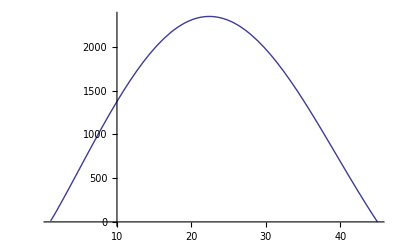

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,2.86628×10^-10},{44.8,2.95385×10^-10},{44.6,3.02082×10^-10},{44.4,3.08788×10^-10},{44.2,3.15664×10^-10},{44.,3.22709×10^-10},{43.8,3.30091×10^-10},{43.6,3.36694×10^-10},{43.4,3.44923×10^-10},{43.2,3.52488×10^-10},{43.,3.60886×10^-10},{42.8,3.68832×10^-10},{42.6,3.772×10^-10},{42.4,3.85808×10^-10},{42.2,3.94604×10^-10},{42.,4.03645×10^-10},{41.8,4.12892×10^-10},{41.6,4.22385×10^-10},{41.4,4.32286×10^-10},{41.2,4.42149×10^-10},{41.,4.52351×10^-10},{40.8,4.62854×10^-10},{40.6,4.73626×10^-10},{40.4,4.84684×10^-10},{40.2,4.96014×10^-10},{40.,5.07636×10^-10},{39.8,5.20441×10^-10},{39.6,5.24938×10^-10},{39.4,5.43985×10^-10},{39.2,5.57244×10^-10},{39.,5.70512×10^-10},{38.8,5.84024×10^-10},{38.6,5.97937×10^-10},{38.4,6.12207×10^-10},{38.2,6.26907×10^-10},{38.,6.41916×10^-10},{37.8,6.57328×10^-10},{37.6,6.75082×10^-10},{37.4,6.89108×10^-10},{37.2,7.06085×10^-10},{37.,7.23195×10^-10},{36.8,7.40752×10^-10},{36.6,7.58779×10^-10},{36.4,7.77323×10^-10},{36.2,7.96288×10^-10},{36.,8.15777×10^-10},{35.8,8.3578×10^-10},{35.6,8.56318×10^-10},{35.4,8.77363×10^-10},{35.2,8.99025×10^-10},{35.,9.22047×10^-10},{34.8,9.43995×10^-10},{34.6,9.67427×10^-10},{34.4,9.91476×10^-10},{34.2,1.01605×10^-9},{34.,1.04133×10^-9},{33.8,1.06731×10^-9},{33.6,1.09396×10^-9},{33.4,1.12127×10^-9},{33.2,1.17143×10^-9},{33.,1.17811×10^-9},{32.8,1.2077×10^-9},{32.6,1.23798×10^-9},{32.4,1.26935×10^-9},{32.2,1.30099×10^-9},{32.,1.3337×10^-9},{31.8,1.36201×10^-9},{31.6,1.40148×10^-9},{31.4,1.43702×10^-9},{31.2,1.47362×10^-9},{31.,1.51041×10^-9},{30.8,1.54845×10^-9},{30.6,1.58712×10^-9},{30.4,1.62749×10^-9},{30.2,1.6685×10^-9},{30.,1.71049×10^-9},{29.8,1.75352×10^-9},{29.6,1.79761×10^-9},{29.4,1.84273×10^-9},{29.2,1.88895×10^-9},{29.,1.93623×10^-9},{28.8,1.97604×10^-9},{28.6,2.03417×10^-9},{28.4,2.08477×10^-9},{28.2,2.1366×10^-9},{28.,2.19081×10^-9},{27.8,2.24338×10^-9},{27.6,2.29863×10^-9},{27.4,2.35487×10^-9},{27.2,2.41224×10^-9},{27.,2.47081×10^-9},{26.8,2.53048×10^-9},{26.6,2.59143×10^-9},{26.4,2.65294×10^-9},{26.2,2.71551×10^-9},{26.,2.77951×10^-9},{25.8,2.84427×10^-9},{25.6,2.90989×10^-9},{25.4,2.97631×10^-9},{25.2,3.04349×10^-9},{25.,3.1113×10^-9},{24.8,3.17969×10^-9},{24.6,3.24849×10^-9},{24.4,3.31755×10^-9},{24.2,3.38674×10^-9},{24.,3.45588×10^-9},{23.8,3.52495×10^-9},{23.6,3.59269×10^-9},{23.4,3.66096×10^-9},{23.2,3.72712×10^-9},{23.,3.79207×10^-9},{22.8,3.85299×10^-9},{22.6,3.91592×10^-9},{22.4,3.9737×10^-9},{22.2,4.0281×10^-9},{22.,4.07802×10^-9},{21.8,4.12294×10^-9},{21.6,4.15878×10^-9},{21.4,4.19433×10^-9},{21.2,4.21828×10^-9},{21.,4.23224×10^-9},{20.8,4.23481×10^-9},{20.6,4.2243×10^-9},{20.4,4.19764×10^-9},{20.2,4.15442×10^-9},{20.,4.09024×10^-9},{19.8,4.00045×10^-9},{19.6,3.88168×10^-9},{19.4,3.72997×10^-9},{19.2,3.53732×10^-9},{19.,3.30338×10^-9},{18.8,3.01327×10^-9},{18.6,2.76289×10^-9},{18.4,2.23433×10^-9},{18.2,1.71969×10^-9},{18.,1.10447×10^-9},{17.8,3.37485×10^-10},{17.6,-5.19224×10^-10},{17.4,-1.57637×10^-9},{17.2,-2.84017×10^-9},{17.,-4.35105×10^-9},{16.8,-6.18508×10^-9},{16.6,-8.3254×10^-9},{16.4,-1.09242×10^-8},{16.2,-1.40448×10^-8},{16.,-1.78299×10^-8},{15.8,-2.23401×10^-8},{15.6,-2.78238×10^-8},{15.4,-3.44701×10^-8},{15.2,-4.25497×10^-8},{15.,-5.24006×10^-8},{14.8,-6.44382×10^-8},{14.6,-7.92059×10^-8},{14.4,-9.73669×10^-8},{14.2,-1.19775×10^-7},{14.,-1.47527×10^-7},{13.8,-1.81995×10^-7},{13.6,-2.24944×10^-7},{13.4,-2.78653×10^-7},{13.2,-3.4605×10^-7},{13.,-4.30911×10^-7},{12.8,-5.38125×10^-7},{12.6,-6.74077×10^-7},{12.4,-8.47046×10^-7},{12.2,-1.06788×10^-6},{12.,-1.35084×10^-6},{11.8,-1.7146×10^-6},{11.6,-2.18401×10^-6},{11.4,-2.79166×10^-6},{11.2,-3.58119×10^-6},{11.,-4.61026×10^-6},{10.8,-5.95617×10^-6},{10.6,-7.72229×10^-6},{10.4,-0.0000100473},{10.2,-0.0000131179},{10.,-0.0000171852}}

```mathematica
(*The imaginary part vs the radius*)
```

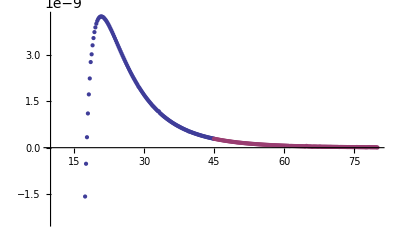

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

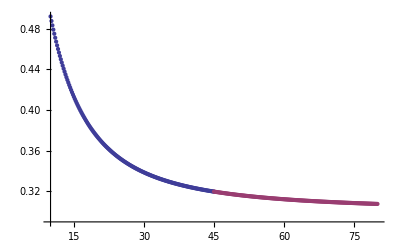

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```